# Evaluation of Quantum-Like Normal Form Approach

```mathematica
(* load quantum model *)
```

```mathematica
Get["/Users/162191/Documents/GitHub/quantum_international_interaction_game/Norm_Form/quantum_normal_form_model.m"];
```

## Experiment 1: Testing on Imbalanced Dataset

### Load Data

```mathematica
data=Import["/Users/162191/Documents/GitHub/quantum_international_interaction_game/Norm_Form/first_dataset_with_SQ.csv","CSV","HeaderLines"->1];
dataset=Dataset[Association@@@(Rule@@@Transpose[{{"Agent1","Agent2","wrTu1sq","wrTu1ac1","wrTu1ac2","wrTu1neg","wrTu1cp1","wrTu1cp2","wrTu1wr1","wrTu1wr2","wrTu2sq","wrTu2ac2","wrTu2ac1","wrTu2neg","wrTu2cp2","wrTu2cp1","wrTu2wr2","wrTu2wr1","groundtruth"},#}]&/@data)];
```

```mathematica
preparedData = PrepareDataset[dataset];
```

### Params

```mathematica
lambda = 1.0;
maxIter = 200;
threshold = 0.00001;
verboseMode = False;
```

### Searching for Optimal Params: Resampling over the full dataset with GridSize 5

Using random sampling strategy with 750 samples

New best accuracy found: 0.0852197 (64 correct out of 751) with phases: {2.31923,3.81975,4.17519,3.73669}

New best accuracy found: 0.103862 (78 correct out of 751) with phases: {5.15907,0.330041,0.22437,5.31183}

New best accuracy found: 0.105193 (79 correct out of 751) with phases: {1.59812,5.60207,1.51828,0.600164}

New best accuracy found: 0.122503 (92 correct out of 751) with phases: {0.232415,6.11853,3.63077,5.70844}

New best accuracy found: 0.126498 (95 correct out of 751) with phases: {2.46137,2.09736,3.13254,2.80756}

Progress: 10% complete

Progress: 20% complete

Progress: 30% complete

Progress: 40% complete

Progress: 50% complete

Progress: 60% complete

Progress: 70% complete

Progress: 80% complete

New best accuracy found: 0.12783 (96 correct out of 751) with phases: {4.82421,5.36694,3.28313,2.56993}

Progress: 90% complete

Progress: 100% complete

{4.82421,5.36694,3.28313,2.56993}

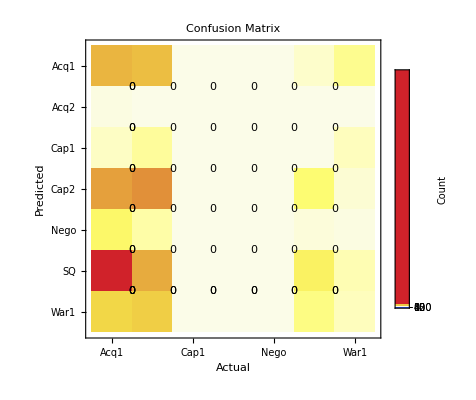
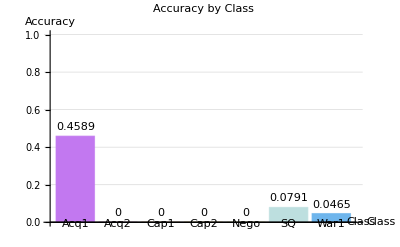
Model Performance with Phases: {4.82421, 5.36694, 3.28313, 2.56993}

Overall Performance Metrics:
Accuracy | 0.1238
Macro-Average Precision | 0.1064
Macro-Average Recall | 0.0835
Macro-Average F1 | 0.0661
Weighted Average F1 | 0.1069

Performance by Outcome Category:
Category | Actual | Predicted | Correct | Precision | Recall | F1 Score
Acq1 | 146 | 375 | 67 | 0.1787 | 0.4589 | 0.2572
Acq2 | 1 | 291 | 0 | 0 | 0 | 0.0000
Cap1 | 20 | 0 | 0 | 0.0000 | 0 | 0.0000
Cap2 | 174 | 0 | 0 | 0.0000 | 0 | 0.0000
Nego | 28 | 0 | 0 | 0.0000 | 0 | 0.0000
SQ | 253 | 52 | 20 | 0.3846 | 0.0791 | 0.1311
War1 | 129 | 33 | 6 | 0.1818 | 0.0465 | 0.0741

Confusion Matrix Analysis:
-Graphics-
-Graphics-
Category | Actual Count | Predicted Count | Correct | Accuracy
Acq1 | 146 | 375 | 67 | 0.4589
Acq2 | 1 | 291 | 0 | 0
Cap1 | 20 | 0 | 0 | 0
Cap2 | 174 | 0 | 0 | 0
Nego | 28 | 0 | 0 | 0
SQ | 253 | 52 | 20 | 0.0791
War1 | 129 | 33 | 6 | 0.0465
Overall Accuracy: 0.1238

```mathematica
optimalResult=FindOptimalPhases[preparedData,lambda,5,"RandomSampling",750,maxIter,threshold,verboseMode];
bestPhases=optimalResult["BestPhases"];
Print[bestPhases];
GetModelMetrics[preparedData, lambda,bestPhases]
```

### Searching for Optimal Params: Resampling over the full dataset with GridSize 10

```mathematica
optimalResult=FindOptimalPhases[preparedData,lambda,10,"RandomSampling",750,maxIter,threshold,verboseMode];
bestPhases=optimalResult["BestPhases"];
Print[bestPhases];
GetModelMetrics[preparedData, lambda,bestPhases]
```

Using random sampling strategy with 750 samples

New best accuracy found: 0.0932091 (70 correct out of 751) with phases: {5.60959,4.79256,1.80621,1.81403}

New best accuracy found: 0.105193 (79 correct out of 751) with phases: {2.92642,6.10593,1.6467,6.21155}

New best accuracy found: 0.126498 (95 correct out of 751) with phases: {2.83846,0.0845882,3.12186,2.50178}

Progress: 10% complete

Progress: 20% complete

Progress: 30% complete

### Searching for Optimal Params: GridSearch over the full dataset Grid size 5

```mathematica
optimalResult=FindOptimalPhases[preparedData,lambda,5,"RandomSampling",750,maxIter,threshold,verboseMode];
bestPhases=optimalResult["BestPhases"];
Print[bestPhases];
GetModelMetrics[preparedData, lambda,bestPhases]
```

### Searching for Optimal Params: GridSearch over the full dataset Grid size 8

```mathematica
optimalResult=FindOptimalPhases[preparedData,lambda,8,"GridSearch"];
bestPhases=optimalResult["BestPhases"];
Print[bestPhases];
GetModelMetrics[preparedData, lambda,bestPhases]
```

### Searching for Optimal Params: GridSearch over the full dataset Grid size 10

```mathematica
optimalResult=FindOptimalPhases[preparedData,lambda,10,"GridSearch"];
bestPhases=optimalResult["BestPhases"];
Print[bestPhases];
GetModelMetrics[preparedData, lambda,bestPhases]
```

## Experiment 2: Testing on Balanced Dataset

```mathematica
data=Import["/Users/162191/Documents/GitHub/quantum_international_interaction_game/Norm_Form/balanced_data.csv","CSV","HeaderLines"->1];
dataset=Dataset[Association@@@(Rule@@@Transpose[{{"Agent1","Agent2","wrTu1sq","wrTu1ac1","wrTu1ac2","wrTu1neg","wrTu1cp1","wrTu1cp2","wrTu1wr1","wrTu1wr2","wrTu2sq","wrTu2ac2","wrTu2ac1","wrTu2neg","wrTu2cp2","wrTu2cp1","wrTu2wr2","wrTu2wr1","groundtruth"},#}]&/@data)];

preparedData = PrepareDataset[dataset];

Length[preparedData]
```

### Params

```mathematica
lambda = 1.0;
maxIter = 200;
threshold = 0.000001;
verboseMode = False;
```

### Searching for Optimal Params: Resampling over the full dataset with GridSize 5

```mathematica
optimalResult=FindOptimalPhases[preparedData,lambda,5,"RandomSampling",750,maxIter,threshold,verboseMode];
bestPhases=optimalResult["BestPhases"];
Print[bestPhases];
GetModelMetrics[preparedData, lambda,bestPhases]
```

### Searching for Optimal Params: Resampling over the full dataset with GridSize 10

```mathematica
optimalResult=FindOptimalPhases[preparedData,lambda,10,"RandomSampling",750,maxIter,threshold,verboseMode];
bestPhases=optimalResult["BestPhases"];
Print[bestPhases];
GetModelMetrics[preparedData, lambda,bestPhases]
```

### Searching for Optimal Params: GridSearch over the full dataset Grid size 5

```mathematica
optimalResult=FindOptimalPhases[preparedData,lambda,5,"RandomSampling",750,maxIter,threshold,verboseMode];
bestPhases=optimalResult["BestPhases"];
Print[bestPhases];
GetModelMetrics[preparedData, lambda,bestPhases]
```

### Searching for Optimal Params: GridSearch over the full dataset Grid size 8

```mathematica
optimalResult=FindOptimalPhases[preparedData,lambda,8,"GridSearch"];
bestPhases=optimalResult["BestPhases"];
Print[bestPhases];
GetModelMetrics[preparedData, lambda,bestPhases]
```

### Searching for Optimal Params: GridSearch over the full dataset Grid size 10

```mathematica
optimalResult=FindOptimalPhases[preparedData,lambda,10,"GridSearch"];
bestPhases=optimalResult["BestPhases"];
Print[bestPhases];
GetModelMetrics[preparedData, lambda,bestPhases]
```